FittedModel[7.21857×10^-10+1.13793×10^-9 x]

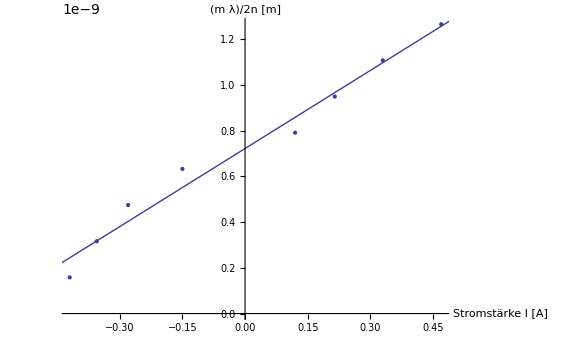

```mathematica
(* Aufgabe 2.1 *)
aufgabe21[m_]=(m*632.8*10^-9)/4000;
punkte={{-0.42,aufgabe21[1]},{-0.355,aufgabe21[2]},{-0.28, aufgabe21[3]},{-0.15,aufgabe21[4]}, {0.12, aufgabe21[5]},{0.215,aufgabe21[6]},{0.33, aufgabe21[7]},{0.47,aufgabe21[8]}};

model=LinearModelFit[punkte,x,x]
Show[ListPlot[punkte],Plot[model["BestFit"],{x,-0.5,0.5}],AxesLabel->{"Stromstärke I [A]", "(m λ)/2n [m]"}]
```

FittedModel[9.65714×10^-7+4.97143×10^-7 x]

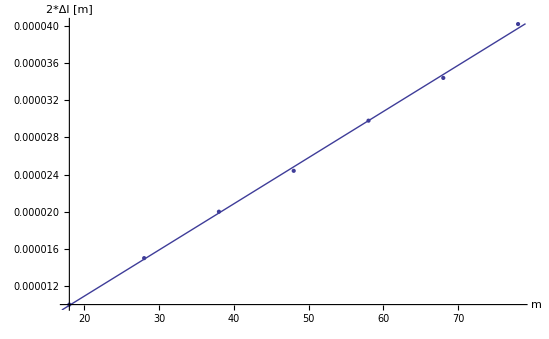

```mathematica
messungen={{18,2*5*10^(-6)},{28,2*7.5*10^(-6)},{38,2*10*10^(-6)},{48,2*12.2*10^(-6)},{58,2*14.9*10^(-6)},{68,2*17.2*10^(-6)},{78,2*20.1*10^(-6)}};
model1 =LinearModelFit[messungen,x,x]
Show[ListPlot[messungen],Plot[model1["BestFit"],{x,17,79}],AxesLabel->{"m", "2*Δl [m]"}]
```

```mathematica
(*interferometrisch *)
15.7*497*10^(-9)/(2*15)
(*klassisch*)
5.19*10^(-6)/15
```

2.60097×10^-7

3.46×10^-7